## 2.2 e)

```mathematica
Solve[{y==0,-Sin[x]-σ*y==0 }](*To take the fixed points*)
```

{{y→0,x→ConditionalExpression[2 π C[1], C[1]∈ℤ]},{y→0,x→ConditionalExpression[π+2 π C[1], C[1]∈ℤ]}}

```mathematica
(*From above we have fixed points when y==0 and x can take values such as 2π*constant or π + 2π*constant for instace. We should limit our investigation so -π<x<=π so we can choose the fixed points (0,0) and (π,0) which is when c1=0 *)
```

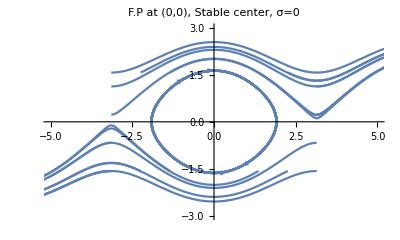

```mathematica
xMin = -π;
xMax = π;
yMin = -π/2;
yMax = π/2;
tMin = 0;
tMax = 20;
systemSolver[x0_,y0_]:=Table[NDSolve[{D[x[t],t]==y[t], D[y[t],t]==-Sin[x[t]]-σ y[t],x[0]==x0,y[0]==y0},{x[t],y[t]},{t,tMin,tMax}],{σ,{0}}];

table1 = Table[{xMin,y},{y,yMin,yMax,0.9}];
table2 = Table[{xMax,y},{y,yMin,yMax,0.9}];
table3 = Table[{x,yMin},{x,xMin,xMax,0.9}];
table4 = Table[{x,yMax},{x,xMin,xMax,0.9}];
initialConditions = Join[table1,table2, table3,table4];
plot=Table[ParametricPlot[Evaluate[{x[t],y[t]}/.systemSolver[initialConditions[[i,1]],initialConditions[[i,2]]]],{t,tMin,tMax}, PlotRange->{{-5,5},{-3,3}},
PlotLabel->"F.P at (0,0), Stable center, σ=0"]/.Line[x_]:>{Arrowheads[{0,0.045,0.045,0.045,0}],Arrow[x]},{i,Length[initialConditions]}];
Show[{plot}]
```

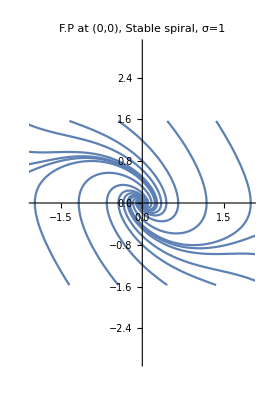

```mathematica
systemSolver[x0_,y0_]:=Table[NDSolve[{D[x[t],t]==y[t], D[y[t],t]==-Sin[x[t]]-σ y[t],x[0]==x0,y[0]==y0},{x[t],y[t]},{t,tMin,tMax}],{σ,{1}}];

table1 = Table[{xMin,y},{y,yMin,yMax,0.9}];
table2 = Table[{xMax,y},{y,yMin,yMax,0.9}];
table3 = Table[{x,yMin},{x,xMin,xMax,0.9}];
table4 = Table[{x,yMax},{x,xMin,xMax,0.9}];
initialConditions = Join[table1,table2, table3,table4];
plot=Table[ParametricPlot[Evaluate[{x[t],y[t]}/.systemSolver[initialConditions[[i,1]],initialConditions[[i,2]]]],{t,tMin,tMax}, PlotRange->{{-2,2},{-3,3}},
PlotLabel->"F.P at (0,0), Stable spiral, σ=1"]/.Line[x_]:>{Arrowheads[{0,0.045,0.045,0.045,0}],Arrow[x]},{i,Length[initialConditions]}];
Show[{plot}]
```

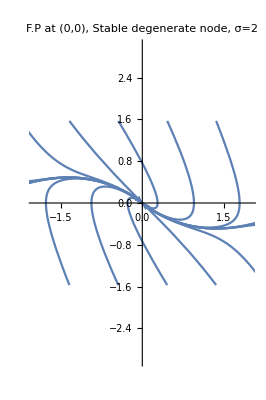

```mathematica
systemSolver[x0_,y0_]:=Table[NDSolve[{D[x[t],t]==y[t], D[y[t],t]==-Sin[x[t]]-σ y[t],x[0]==x0,y[0]==y0},{x[t],y[t]},{t,tMin,tMax}],{σ,{2}}];

table1 = Table[{xMin,y},{y,yMin,yMax,0.9}];
table2 = Table[{xMax,y},{y,yMin,yMax,0.9}];
table3 = Table[{x,yMin},{x,xMin,xMax,0.9}];
table4 = Table[{x,yMax},{x,xMin,xMax,0.9}];
initialConditions = Join[table1,table2, table3,table4];
plot=Table[ParametricPlot[Evaluate[{x[t],y[t]}/.systemSolver[initialConditions[[i,1]],initialConditions[[i,2]]]],{t,tMin,tMax}, PlotRange->{{-2,2},{-3,3}},
PlotLabel->"F.P at (0,0), Stable degenerate node, σ=2"]/.Line[x_]:>{Arrowheads[{0,0.045,0.045,0.045,0}],Arrow[x]},{i,Length[initialConditions]}];
Show[{plot}]
```

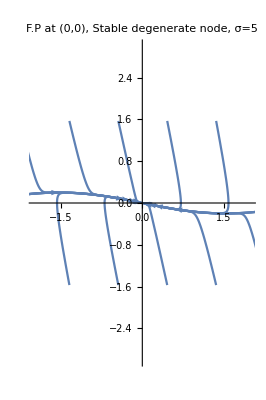

```mathematica
systemSolver[x0_,y0_]:=Table[NDSolve[{D[x[t],t]==y[t], D[y[t],t]==-Sin[x[t]]-σ y[t],x[0]==x0,y[0]==y0},{x[t],y[t]},{t,tMin,tMax}],{σ,{5}}];

table1 = Table[{xMin,y},{y,yMin,yMax,0.9}];
table2 = Table[{xMax,y},{y,yMin,yMax,0.9}];
table3 = Table[{x,yMin},{x,xMin,xMax,0.9}];
table4 = Table[{x,yMax},{x,xMin,xMax,0.9}];
initialConditions = Join[table1,table2, table3,table4];
plot=Table[ParametricPlot[Evaluate[{x[t],y[t]}/.systemSolver[initialConditions[[i,1]],initialConditions[[i,2]]]],{t,tMin,tMax}, PlotRange->{{-2,2},{-3,3}},
PlotLabel->"F.P at (0,0), Stable degenerate node, σ=5"]/.Line[x_]:>{Arrowheads[{0,0.045,0.045,0.045,0}],Arrow[x]},{i,Length[initialConditions]}];
Show[{plot}]
```

```mathematica
table = TextGrid[{{"fix point (x,y)", "(0,0)"},
{"σ=0", "Stable center"},
{"σ=1", "Stable spiral"},
{"σ=2", "Stable degenerate node"},
{"σ=5", "Stable degenerate node"}},Frame->All]
```

fix point (x,y) | (0,0)
σ=0 | Stable center
σ=1 | Stable spiral
σ=2 | Stable degenerate node
σ=5 | Stable degenerate node